Jai Prasadh
HW 7 Problem 4

```mathematica
Clear[H, L, x, n]
part1 = (2/L) Integrate[(3  H x/(2*L)) Sin[n Pi x/L],{x,0,2  L/3}]
```

(H (-2 n π Cos[(2 n π)/3]+3 Sin[(2 n π)/3]))/(n^2 π^2)

```mathematica
part2=(2/L) Integrate[(3 H -(3  H x/L)) Sin[n Pi x/L],{x,2  L/3,L}]
```

(2 H (n π Cos[(2 n π)/3]+3 Sin[(2 n π)/3]-3 Sin[n π]))/(n^2 π^2)

```mathematica
a[n_]:=H/(n^2 π^2) (9 Sin[(2 n π)/3]-6 Sin[n π]);
TableForm[Table[{"n =" , n, a[n]},{n,1,5}]]
```

n = | 1 | (9 √3 H)/(2 π^2)
n = | 2 | -(9 √3 H)/(8 π^2)
n = | 3 | 0
n = | 4 | (9 √3 H)/(32 π^2)
n = | 5 | -(9 √3 H)/(50 π^2)

```mathematica
Sum[a[n] Sin[(n Pi x )/L],{n,1,5}]
```

(9 √3 H Sin[(π x)/L])/(2 π^2)-(9 √3 H Sin[(2 π x)/L])/(8 π^2)+(9 √3 H Sin[(4 π x)/L])/(32 π^2)-(9 √3 H Sin[(5 π x)/L])/(50 π^2)

```mathematica
L=0.6;
H=0.001;
mu=0.0018;
T0=160;
v0=(T0/mu)^0.5;
w1=v0 Pi/L;
T=2 Pi/w1;
y[x_,0]:=Sum[a[n] Sin[n Pi x/L] ,{n,nmax}];
```

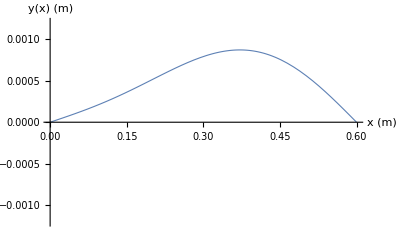

```mathematica
nmax=3;
Plot[y[x,0], {x,0,L},AxesLabel->{"x (m)","y(x) (m)"},PlotStyle->Thickness[0.002],PlotRange->{-1.2 H,1.2 H}]
```

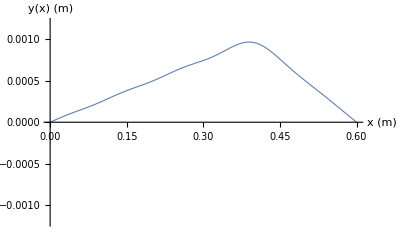

```mathematica
nmax=10;
Plot[y[x,0], {x,0,L},AxesLabel->{"x (m)","y(x) (m)"},PlotStyle->Thickness[0.002],PlotRange->{-1.2 H,1.2 H}]
```

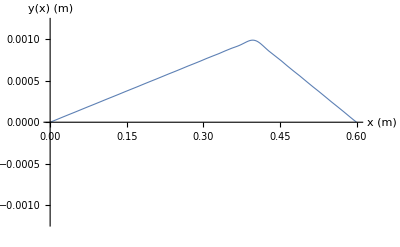

```mathematica
nmax=30;
Plot[y[x,0], {x,0,L},AxesLabel->{"x (m)","y(x) (m)"},PlotStyle->Thickness[0.002],PlotRange->{-1.2 H,1.2 H}]
```

```mathematica
At least 30 terms are needed to provide a good approximation.
```

```mathematica
y[x_,t_]:=Sum[a[n] Sin[n Pi x/L] Cos[n w1 t],{n,nmax}]
```

This is the displacement at all positions and times, assuming nmax is large enough.

```mathematica
nmax = 50;
```

```mathematica
Animate[Plot[y[x,t],{x,0,L},AxesLabel->{"x (m)","y(x) (m)"},PlotStyle->Thickness[0.002],PlotRange->{-1.2 H,1.2 H},AxesStyle->Directive[Thickness[0.002],14]],{t,0,T},AnimationRunning->False,AnimationRepetitions->100]
```

```mathematica
Animate[Plot[y[x,t],{x,0,L},AxesLabel->{"x (m)","y(x) (m)"},PlotStyle->Thickness[0.002],PlotRange->{-1.2 H,1.2 H},AxesStyle->Directive[Thickness[0.002],14]],{t,0,T},AnimationRunning->False,AnimationRepetitions->100]
```

```mathematica
Animate[Plot[y[x,t],{x,0,L},AxesLabel->{"x (m)","y(x) (m)"},PlotStyle->Thickness[0.002],PlotRange->{-1.2 H,1.2 H},AxesStyle->Directive[Thickness[0.002],14]],{t,0,T},AnimationRunning->False,AnimationRepetitions->100]
```